```mathematica
adjMat=Import["E:\\Downloads\\projections_12.xlsx"]//First//N;
adjMat=Replace[adjMat,""->0.,Infinity];
```

```mathematica
adjMat//MatrixForm
```

(0. | 0.03 | 0. | 1.6868 | 0.0121 | 0.088 | 0.113 | 2.627 | 0. | 0. | 0. | 0.
0.0633 | 0. | 0. | 0.035 | 0.0207 | 0.0001 | 0. | 0.0451 | 0. | 0. | 0. | 0.
0.0009 | 0.0222 | 0. | 0.0943 | 0.0423 | 0.0477 | 0.0188 | 0.1028 | 0. | 0. | 0. | 0.
0.1967 | 0. | 0. | 0. | 0. | 0.0536 | 0.0189 | 0.1894 | 0. | 0. | 0. | 0.
0.0118 | 0.0023 | 0.3341 | 0.282 | 0. | 0.0972 | 0.0029 | 0.0567 | 0. | 0. | 0. | 0.
0.0009 | 0.0008 | 0.1256 | 0.0684 | 0.0547 | 0. | 0.0041 | 0.1334 | 0. | 0. | 0. | 0.
0.016 | 0.002 | 0.3351 | 0.1856 | 0.1624 | 0.3697 | 0. | 0.1541 | 0. | 0.0023 | 0. | 0.
0. | 0. | 0. | 0.3727 | 0.0108 | 0.0436 | 0.0761 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0003 | 0. | 0. | 0.0194 | 0.339 | 0.339
0. | 0. | 0. | 0. | 0. | 0. | 0.0031 | 0. | 0.013 | 0. | 0.013 | 0.013
0. | 0. | 0. | 0.0255 | 0. | 0. | 0.0003 | 0. | 0.339 | 0.0194 | 0. | 0.339
0. | 0. | 0. | 0.0255 | 0. | 0. | 0.0003 | 0. | 0.339 | 0.0194 | 0.339 | 0.)

```mathematica
1/Replace[adjMat,0.->Infinity,Infinity];
adjMat2=Replace[%,0->Infinity,Infinity];
adjMat2//MatrixForm
```

(∞ | 33.3333 | ∞ | 0.592839 | 82.6446 | 11.3636 | 8.84956 | 0.380662 | ∞ | ∞ | ∞ | ∞
15.7978 | ∞ | ∞ | 28.5714 | 48.3092 | 10000. | ∞ | 22.1729 | ∞ | ∞ | ∞ | ∞
1111.11 | 45.045 | ∞ | 10.6045 | 23.6407 | 20.9644 | 53.1915 | 9.72763 | ∞ | ∞ | ∞ | ∞
5.08388 | ∞ | ∞ | ∞ | ∞ | 18.6567 | 52.9101 | 5.27983 | ∞ | ∞ | ∞ | ∞
84.7458 | 434.783 | 2.99312 | 3.5461 | ∞ | 10.2881 | 344.828 | 17.6367 | ∞ | ∞ | ∞ | ∞
1111.11 | 1250. | 7.96178 | 14.6199 | 18.2815 | ∞ | 243.902 | 7.49625 | ∞ | ∞ | ∞ | ∞
62.5 | 500. | 2.98418 | 5.38793 | 6.15764 | 2.7049 | ∞ | 6.48929 | ∞ | 434.783 | ∞ | ∞
∞ | ∞ | ∞ | 2.68312 | 92.5926 | 22.9358 | 13.1406 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3333.33 | ∞ | ∞ | 51.5464 | 2.94985 | 2.94985
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 322.581 | ∞ | 76.9231 | ∞ | 76.9231 | 76.9231
∞ | ∞ | ∞ | 39.2157 | ∞ | ∞ | 3333.33 | ∞ | 2.94985 | 51.5464 | ∞ | 2.94985
∞ | ∞ | ∞ | 39.2157 | ∞ | ∞ | 3333.33 | ∞ | 2.94985 | 51.5464 | 2.94985 | ∞)

```mathematica
adjMatLog=Log[adjMat2+1];
adjMatLog//MatrixForm
```

(∞ | 3.53612 | ∞ | 0.465518 | 4.42658 | 2.51476 | 2.28743 | 0.322563 | ∞ | ∞ | ∞ | ∞
2.82125 | ∞ | ∞ | 3.38681 | 3.89811 | 9.21044 | ∞ | 3.14299 | ∞ | ∞ | ∞ | ∞
7.01402 | 3.82962 | ∞ | 2.45139 | 3.2044 | 3.08942 | 3.99252 | 2.37282 | ∞ | ∞ | ∞ | ∞
1.80564 | ∞ | ∞ | ∞ | ∞ | 2.97842 | 3.98732 | 1.83734 | ∞ | ∞ | ∞ | ∞
4.45139 | 6.07714 | 1.38457 | 1.51427 | ∞ | 2.42375 | 5.84594 | 2.92513 | ∞ | ∞ | ∞ | ∞
7.01402 | 7.1317 | 2.19297 | 2.74854 | 2.95915 | ∞ | 5.50086 | 2.13963 | ∞ | ∞ | ∞ | ∞
4.15104 | 6.21661 | 1.38233 | 1.85441 | 1.96818 | 1.30966 | ∞ | 2.01347 | ∞ | 6.07714 | ∞ | ∞
∞ | ∞ | ∞ | 1.30376 | 4.53895 | 3.17537 | 2.64905 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 8.11203 | ∞ | ∞ | 3.9617 | 1.37368 | 1.37368
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 5.77945 | ∞ | 4.35572 | ∞ | 4.35572 | 4.35572
∞ | ∞ | ∞ | 3.69426 | ∞ | ∞ | 8.11203 | ∞ | 1.37368 | 3.9617 | ∞ | 1.37368
∞ | ∞ | ∞ | 3.69426 | ∞ | ∞ | 8.11203 | ∞ | 1.37368 | 3.9617 | 1.37368 | ∞)

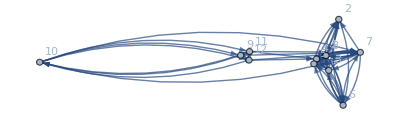

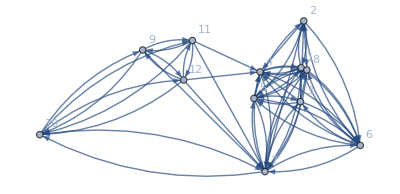

```mathematica
g=WeightedAdjacencyGraph[adjMat2,VertexLabels->Table[i->i,{i,1,12}],GraphLayout->{"SpringEmbedding","EdgeWeighted"->True,"MaxIteration"->1000000}]
gLog=WeightedAdjacencyGraph[adjMatLog,VertexLabels->Table[i->i,{i,1,12}],GraphLayout->{"SpringEmbedding","EdgeWeighted"->True,"MaxIteration"->1000000}]
```

```mathematica
coord = GraphEmbedding[gLog];
%//MatrixForm
```

(2.55985 | 1.0185
2.58553 | 1.47713
2.55355 | 0.685815
2.15735 | 0.977803
2.09719 | 0.717622
3.13865 | 0.256719
2.20585 | 0.
2.61624 | 0.996614
1.00805 | 1.19254
0. | 0.362407
1.49487 | 1.28542
1.40947 | 0.898111)

```mathematica
Export["E:\\Downloads\\coordinates.mat",coord]
```

E:\Downloads\coordinates.mat